```mathematica
(*Define parameters*)a=0.4;  (*Adjust this as needed*)
timeSteps=10000;  (*Simulation length*)
betaStart=1;  (*Starting β value,indicating symmetric information level*)
betaEnd=0.4;  (*End β value to simulate market collapse*)
betaDecay=(betaStart-betaEnd)/timeSteps;  (*Decay rate of β*)

(*Initialize state probabilities:Assume starting in High Quality*)
state="H";
statesHistory={state};

(*Simulation*)
For[t=1,t<=timeSteps,t++,β=betaStart-t*betaDecay;
transitionMatrix={{β-a,1-(β-a)},{β-a,1-(β-a)}};
(*Choose next state based on current state and transition probabilities*)stateProbabilities=If[state=="H",transitionMatrix[[1]],transitionMatrix[[2]]];
state=If[RandomReal[]<stateProbabilities[[1]],"H","L"];
AppendTo[statesHistory,state];]

(*Output the history of states to analyze the market behavior over time*)
statesHistory
```

{H,L,L,H,L,L,H,H,L,H,H,H,L,L,H,L,L,L,L,H,H,H,H,H,L,H,H,H,L,L,H,L,L,H,H,L,L,L,H,L,H,H,H,H,L,H,H,H,H,L,H,H,H,L,H,H,H,L,H,H,H,H,L,L,H,L,H,H,H,H,L,H,L,L,H,L,L,H,H,H,H,L,L,H,H,H,L,H,L,H,H,L,L,H,L,H,L,H,H,L,H,H,L,L,L,H,H,L,H,H,L,L,H,H,L,L,H,L,H,L,L,H,L,L,L,L,H,H,L,L,H,H,H,H,H,H,L,H,L,L,H,H,L,H,H,H,H,H,H,L,H,L,H,L,L,H,L,L,H,H,H,L,H,L,L,L,L,L,H,L,H,H,L,H,H,H,H,H,L,H,H,L,H,H,H,L,H,H,L,H,H,H,H,L,H,L,H,H,L,H,L,L,L,L,H,H,L,H,H,L,L,H,H,H,H,H,H,H,L,L,H,L,H,L,L,L,L,H,H,H,L,L,H,L,H,L,H,L,H,L,H,L,H,L,L,L,L,H,L,H,L,L,H,L,H,L,H,H,H,L,H,H,H,H,L,H,L,H,H,L,H,H,H,H,H,L,H,H,L,L,H,H,L,L,L,H,H,H,L,L,H,H,H,H,L,L,L,H,L,L,H,H,L,H,L,L,L,H,H,L,L,H,H,L,H,L,H,H,H,H,L,L,H,H,H,L,H,L,L,L,L,L,L,L,L,L,H,L,L,H,L,L,H,L,L,H,L,L,L,H,L,H,H,H,L,L,L,H,L,H,H,H,H,H,L,L,H,H,L,H,H,H,H,L,L,H,L,H,L,L,H,H,H,H,L,L,L,H,H,L,L,L,H,L,L,H,H,L,L,L,H,H,L,H,H,L,H,L,L,H,L,L,H,H,H,H,H,L,L,H,H,H,H,H,L,H,H,H,H,L,H,L,L,H,L,H,H,H,L,H,L,H,H,L,H,H,H,L,H,L,H,H,H,L,H,H,H,L,H,L,H,H,H,L,H,H,H,L,L,L,H,L,H,L,L,H,H,L,L,H,L,H,H,L,H,H,H,H,L,H,H,H,L,H,H,H,L,H,H,L,H,H,H,H,H,H,H,H,H,H,L,H,H,L,H,H,H,H,H,H,H,H,L,H,L,L,L,H,H,H,L,L,L,H,L,H,H,H,L,L,H,H,H,L,L,L,L,H,L,H,L,L,H,L,H,L,L,L,H,H,H,L,H,H,H,H,H,H,H,H,H,L,H,L,H,L,H,L,H,H,H,L,H,L,H,L,H,H,L,H,H,H,L,H,H,L,H,H,L,H,H,H,L,L,L,L,H,H,H,H,L,L,L,H,L,L,L,H,H,H,H,L,L,H,L,L,L,H,H,L,H,L,H,L,H,L,L,H,H,H,H,L,H,H,L,L,H,H,L,L,L,L,H,L,H,L,L,H,H,L,L,H,L,L,L,L,H,L,L,L,H,H,H,H,L,L,H,H,L,H,H,H,H,L,H,H,H,L,H,L,L,H,L,L,H,H,H,H,L,H,H,L,L,L,H,H,H,H,H,H,L,L,H,H,L,H,H,H,H,L,H,L,L,L,L,L,L,H,H,H,H,H,H,H,L,H,H,H,L,H,H,L,L,H,L,H,H,H,H,H,H,H,L,H,L,H,L,L,H,H,L,L,L,H,H,H,L,H,H,H,L,H,L,H,H,H,H,H,H,L,H,L,H,H,H,H,H,H,H,L,L,H,L,H,H,H,H,L,H,L,L,H,L,H,H,H,L,H,H,H,H,H,H,H,H,L,H,H,L,H,L,L,H,H,H,L,L,L,L,H,H,H,H,L,H,L,H,H,L,H,H,L,H,H,H,H,H,H,H,H,H,H,H,H,L,H,H,H,H,L,L,H,H,H,L,H,H,L,L,H,L,H,H,L,H,H,H,H,H,L,H,L,L,H,L,L,L,L,L,L,L,H,L,H,H,L,H,L,H,H,L,L,H,L,H,H,L,L,L,L,H,L,L,L,H,H,H,H,H,H,H,L,L,H,H,H,H,H,H,H,H,L,L,L,H,H,H,L,H,L,L,H,H,H,H,L,H,H,H,L,H,L,H,H,L,H,H,H,L,L,L,H,L,L,L,L,L,L,H,H,L,H,L,H,L,H,L,H,H,H,H,H,L,H,L,L,L,L,L,H,H,H,H,L,L,H,L,H,H,H,H,L,H,H,H,L,L,H,H,L,L,L,H,L,H,L,H,H,L,L,H,L,L,L,L,H,H,L,L,L,H,L,H,L,H,L,H,H,H,H,H,H,H,H,H,L,L,L,L,L,L,L,L,H,L,L,H,L,H,H,H,H,L,H,L,L,L,H,H,H,H,L,L,H,L,L,H,H,L,L,L,H,H,H,L,L,L,H,H,L,H,H,L,L,H,L,H,H,L,L,H,L,L,L,L,L,L,H,H,H,L,H,L,L,L,H,H,L,L,L,L,H,H,H,H,H,L,H,L,L,L,H,H,L,H,H,H,L,H,H,L,H,L,L,H,H,H,H,H,L,L,H,H,H,L,L,L,H,L,H,H,H,L,H,H,L,L,H,H,H,H,H,H,H,L,H,H,H,H,L,L,L,H,L,L,L,L,L,L,H,L,L,H,H,H,H,L,H,H,H,H,H,L,H,H,H,L,L,H,L,L,L,L,H,L,H,L,L,L,L,H,L,L,H,L,H,L,H,H,H,L,H,H,H,L,L,H,H,L,H,H,H,H,L,H,H,H,L,H,H,L,H,H,H,H,H,H,H,L,H,H,L,H,H,H,L,L,L,L,L,L,H,L,L,L,H,L,H,H,L,H,L,H,L,L,L,H,L,H,L,L,L,L,H,H,L,H,H,L,H,L,L,H,L,H,H,L,L,L,H,H,L,L,L,L,H,L,H,L,H,L,H,L,H,H,L,L,L,H,H,L,H,L,L,H,L,H,H,H,H,L,H,H,H,H,L,H,L,L,H,L,L,H,L,H,L,H,H,L,H,L,H,L,H,L,L,H,H,H,H,L,L,H,L,H,H,H,H,H,H,H,L,L,H,L,H,H,H,L,H,H,H,L,H,H,H,H,H,L,L,H,H,H,L,L,L,H,H,L,L,L,L,H,H,L,L,H,L,L,L,L,L,H,L,H,L,H,H,L,H,L,L,L,H,H,L,H,L,H,H,H,L,L,H,H,H,H,L,H,H,L,H,L,L,H,H,H,L,L,L,H,L,H,H,L,L,L,L,H,L,L,H,L,H,H,L,L,L,L,H,H,L,L,L,L,L,H,H,L,H,H,L,H,H,L,L,L,H,H,H,L,L,L,H,L,H,L,L,L,H,H,L,L,H,L,L,L,H,L,L,H,L,L,L,H,H,L,L,H,H,L,H,L,L,H,H,L,H,L,H,H,H,H,H,L,H,H,H,L,H,L,H,L,L,L,L,L,H,H,H,H,L,H,H,L,L,L,H,L,L,H,H,H,L,L,H,H,H,L,H,L,H,H,H,L,L,L,H,H,L,L,H,H,L,H,L,L,L,H,H,H,L,H,H,L,H,H,L,H,L,H,H,H,L,L,L,L,H,H,L,L,L,L,L,H,L,L,H,L,H,H,L,H,H,H,H,L,L,L,H,H,L,L,H,H,L,H,L,H,H,H,H,H,L,L,H,L,H,H,L,L,L,H,H,L,L,L,L,L,H,L,L,L,L,H,L,H,L,L,H,L,H,L,L,L,H,H,H,H,H,H,H,H,L,H,L,L,L,H,H,L,H,H,H,L,L,L,H,L,H,L,H,L,L,L,H,L,H,H,H,L,L,L,H,L,H,L,H,L,H,L,L,L,H,L,H,H,L,H,H,H,L,L,L,H,H,H,L,L,H,L,H,L,L,L,L,H,L,H,H,H,H,H,H,H,L,L,H,L,H,H,H,H,H,H,L,H,L,H,H,H,L,H,L,H,H,L,L,L,H,H,L,L,L,H,H,L,H,H,L,L,L,H,H,L,L,H,H,H,H,L,L,L,H,L,L,H,H,H,L,L,L,L,L,L,L,L,H,H,H,L,L,H,L,L,L,H,L,H,H,L,L,H,H,L,L,H,L,H,L,L,H,H,H,L,H,L,L,L,H,L,H,L,H,H,L,H,L,L,H,L,H,L,L,H,L,L,H,L,H,H,L,L,H,L,L,L,H,H,H,L,H,L,L,L,L,H,L,H,L,L,L,H,H,L,H,L,L,L,L,H,H,L,L,L,H,H,H,L,H,L,H,H,H,H,L,H,L,H,H,L,H,L,L,H,L,H,L,H,L,H,L,L,L,L,L,H,L,L,H,H,H,H,L,H,L,L,H,L,H,H,L,H,H,H,H,H,H,L,H,H,H,L,H,H,L,L,L,L,L,L,H,L,H,L,L,L,L,L,H,H,L,H,H,H,L,L,H,H,L,L,L,L,L,L,H,H,H,H,L,H,H,L,L,H,L,H,H,L,H,L,L,H,H,L,H,L,L,L,L,H,H,L,L,L,L,L,L,L,H,L,H,L,H,H,H,H,L,L,H,H,H,L,H,H,L,H,H,L,L,H,H,H,H,H,L,L,L,H,H,L,H,L,H,L,H,L,H,H,H,L,H,L,L,H,L,L,H,L,L,H,H,L,L,L,L,L,H,L,L,H,L,L,L,H,H,H,L,L,L,H,H,H,H,H,L,L,L,L,H,H,L,H,L,L,H,H,H,L,L,L,L,L,H,L,H,L,H,H,L,H,L,H,L,H,H,H,H,L,H,H,H,H,L,L,H,H,H,L,L,L,H,H,H,L,H,H,L,L,H,L,L,H,H,L,L,H,H,H,L,H,H,L,L,L,L,H,H,H,L,L,L,H,H,H,H,H,L,L,H,L,H,L,H,L,H,H,L,L,L,H,L,L,H,L,L,H,H,L,L,L,H,L,L,H,L,L,L,H,L,H,L,L,H,H,H,L,L,H,H,H,L,L,H,L,H,H,H,H,H,H,H,L,H,L,L,L,H,L,L,L,L,L,L,H,H,H,L,L,L,L,H,L,H,H,H,H,H,L,L,H,L,H,L,L,H,H,H,H,H,L,L,L,H,H,H,L,H,H,L,H,H,L,H,H,L,L,L,L,L,L,H,H,H,L,H,L,H,L,H,H,L,H,L,L,L,L,L,L,H,H,H,L,L,L,L,L,L,H,H,H,L,H,L,H,H,H,H,H,L,H,H,L,L,L,L,H,L,L,L,H,H,L,L,H,H,L,L,L,H,H,H,L,L,L,L,L,L,L,L,H,H,L,H,H,H,L,L,H,H,L,L,L,L,H,L,L,H,L,L,L,H,H,L,H,H,L,L,L,L,L,L,L,H,L,H,H,H,L,L,H,H,H,L,L,H,L,L,H,L,L,L,H,L,L,H,L,H,L,L,H,H,L,H,L,H,L,H,L,H,L,L,H,H,L,L,H,L,L,H,H,H,H,L,H,L,H,L,H,H,L,H,L,L,H,L,L,L,H,H,L,L,H,H,H,H,L,L,L,L,H,H,L,H,H,L,L,H,H,L,L,H,H,H,H,L,L,L,L,H,L,L,H,H,L,H,H,H,L,H,H,H,H,H,L,H,L,H,L,L,H,H,H,L,L,H,H,L,L,L,L,H,H,H,L,L,H,L,L,L,H,L,L,L,H,L,L,H,H,H,L,H,H,H,L,H,L,L,L,H,L,H,L,L,H,H,L,H,L,L,H,H,L,H,H,L,L,L,L,H,H,L,H,L,H,H,L,H,L,L,H,L,L,L,L,H,L,H,L,H,L,H,L,H,L,H,L,L,H,L,L,L,L,H,L,L,H,H,L,H,H,L,L,H,H,L,H,L,L,L,H,H,H,L,H,L,H,L,H,L,L,L,L,L,H,H,L,H,L,L,L,H,L,L,H,H,L,H,H,L,H,L,L,L,L,L,H,L,L,L,H,H,H,H,H,L,L,H,H,H,H,L,H,H,L,H,L,H,H,H,H,L,H,H,H,L,H,L,L,L,H,L,L,L,L,H,H,L,H,H,L,L,H,L,H,H,H,L,L,H,H,H,H,L,L,L,L,L,H,L,L,H,H,H,H,L,L,H,H,L,L,L,L,H,H,H,H,H,H,H,L,H,L,L,L,L,H,L,H,H,L,L,L,H,H,H,H,L,L,L,H,H,L,H,L,L,L,L,H,L,H,H,L,L,H,L,H,L,H,L,H,L,L,L,H,L,L,L,H,L,H,L,L,H,L,L,H,L,L,L,L,L,L,L,H,H,L,L,L,L,L,H,L,H,L,H,L,L,H,H,H,L,H,L,H,L,L,H,L,H,H,H,H,L,L,L,L,L,L,L,L,L,H,H,L,L,H,H,H,H,H,H,L,L,L,H,H,L,H,H,L,L,H,L,H,L,H,L,L,L,L,L,H,H,H,L,L,H,L,H,L,L,L,L,L,H,L,L,L,H,H,H,L,L,L,H,L,L,L,L,H,L,L,L,L,L,L,L,H,L,H,L,L,L,L,L,L,H,L,L,H,L,L,L,L,H,L,L,L,H,H,H,L,L,L,H,L,H,H,H,L,L,H,L,L,H,H,H,H,L,L,L,L,L,L,H,H,L,L,H,L,H,H,H,L,L,H,L,L,H,L,L,L,L,L,L,L,L,H,L,H,H,H,L,L,L,L,H,L,L,H,L,L,H,L,L,L,L,L,L,L,H,L,L,H,H,H,L,L,H,L,L,H,L,H,L,H,L,L,L,L,L,H,H,L,L,L,H,L,L,H,L,L,L,H,H,L,L,L,L,L,H,H,L,L,L,H,H,H,H,L,L,L,L,H,L,H,H,H,L,H,L,L,L,H,L,H,L,L,L,H,L,H,H,L,H,L,L,L,L,L,L,L,L,H,L,H,H,L,H,L,H,H,L,H,L,L,L,L,L,H,L,L,L,H,H,L,L,H,L,L,L,L,L,L,L,L,L,H,L,H,L,L,H,H,L,L,H,H,L,H,L,L,L,L,L,H,L,L,H,L,L,L,H,L,L,H,H,H,H,L,L,H,L,L,H,L,L,L,L,H,H,H,H,L,H,H,L,L,L,L,H,H,H,H,L,H,L,H,H,L,L,L,L,L,L,H,L,L,L,L,L,H,L,L,H,H,L,L,H,H,L,H,H,L,L,H,L,L,H,L,H,L,H,L,L,H,L,H,H,H,L,H,H,L,L,L,H,L,L,L,L,L,H,L,L,L,L,H,L,L,L,H,H,L,H,H,H,H,L,L,L,L,L,H,L,H,L,L,H,H,H,L,L,L,H,L,L,H,H,L,H,H,L,H,L,H,L,L,L,H,L,L,L,H,H,L,H,L,L,L,H,H,L,L,H,H,L,L,H,L,L,H,L,H,L,L,L,H,H,L,L,L,L,L,H,H,H,H,L,H,H,L,H,H,H,L,L,L,L,H,L,H,L,L,L,L,H,L,H,H,L,H,H,L,H,H,L,H,L,H,L,H,L,L,H,H,L,L,H,H,L,L,L,H,L,H,H,H,L,L,L,H,H,L,L,H,H,L,L,H,L,L,L,L,H,L,L,H,L,H,L,L,H,L,H,L,L,H,L,L,L,H,H,L,L,H,L,H,L,L,L,L,L,H,H,H,L,L,H,L,L,L,L,L,H,L,H,H,H,L,L,L,H,L,L,L,L,H,H,L,L,L,L,H,L,H,H,L,L,L,H,L,H,H,L,H,H,H,L,L,H,L,L,L,H,H,L,H,L,H,H,L,L,H,H,L,L,L,L,L,H,H,L,H,H,L,L,L,L,L,L,L,L,H,L,L,L,L,H,H,H,L,L,L,H,L,L,H,L,L,H,H,L,H,H,H,H,L,L,L,L,H,H,L,H,L,H,L,L,H,L,L,L,H,L,L,H,H,L,L,L,L,L,H,L,H,L,L,H,L,L,L,L,L,L,H,H,H,L,L,L,L,L,H,L,L,L,L,H,L,L,L,L,L,H,H,L,H,L,L,L,L,L,L,L,H,H,L,H,H,L,H,H,L,H,L,L,H,H,L,H,H,L,H,L,L,H,L,H,H,L,L,L,L,H,L,H,L,H,H,L,H,L,L,L,L,L,L,L,H,H,H,L,H,L,H,H,L,L,H,L,L,H,L,L,L,L,L,L,L,L,H,H,H,L,H,L,H,L,L,L,L,L,H,H,L,L,L,L,L,L,L,H,L,L,H,L,H,L,L,H,L,L,L,L,H,H,L,H,L,H,H,L,L,H,L,H,L,L,H,H,H,L,H,H,L,L,L,L,L,L,H,L,L,L,L,H,L,H,L,L,H,H,H,L,L,H,H,H,H,L,L,L,L,L,L,H,H,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,H,H,L,L,L,H,L,H,L,L,L,L,L,H,L,L,H,L,L,L,H,L,L,L,L,L,H,L,L,L,L,L,L,L,H,H,L,L,L,L,L,H,H,L,H,L,L,L,H,H,L,H,H,L,H,L,L,L,H,H,H,L,L,L,L,H,H,L,L,H,H,L,L,L,L,H,H,H,L,H,L,L,L,H,H,L,H,H,H,H,L,L,L,H,H,L,L,L,H,L,L,H,H,L,L,H,L,H,L,H,L,H,L,L,L,L,H,L,L,L,L,L,L,H,L,H,L,H,H,H,L,L,H,H,L,H,L,L,H,L,L,H,L,L,H,H,L,L,H,H,L,H,L,L,H,L,H,L,H,H,H,L,H,H,L,L,L,L,H,L,H,L,L,H,L,H,L,L,L,L,H,H,H,L,L,H,L,L,H,L,L,H,L,H,L,H,L,H,L,H,L,H,L,L,H,L,L,H,L,H,L,L,L,H,H,L,H,L,H,H,L,H,H,L,L,H,L,L,L,L,L,H,H,L,H,L,H,L,H,H,L,H,H,H,H,L,L,H,H,L,H,H,L,L,L,H,H,L,L,H,L,L,L,L,L,H,H,L,H,H,L,H,L,H,L,L,H,H,L,H,L,L,L,H,H,L,L,H,L,L,L,L,H,H,H,L,H,H,L,L,L,H,L,L,L,H,L,L,L,H,L,L,L,L,L,H,H,L,H,L,L,L,L,L,L,L,H,H,H,H,L,H,L,H,L,L,H,L,H,L,L,L,L,H,L,L,H,L,H,L,L,L,L,L,L,H,L,L,L,L,H,H,L,L,H,H,H,L,L,L,L,L,H,L,H,H,L,L,L,L,L,H,H,L,H,L,L,L,L,H,L,H,H,L,L,H,H,L,L,L,H,H,L,L,L,H,L,H,H,H,H,L,H,L,L,H,L,L,L,L,H,L,L,H,L,L,L,L,L,L,L,H,L,L,H,L,L,H,L,L,H,L,H,L,L,L,H,L,L,L,L,L,H,L,L,H,H,L,H,L,L,H,H,L,H,L,L,L,H,H,L,L,H,H,L,L,L,L,H,H,L,L,H,H,L,L,L,H,L,L,L,H,L,L,H,L,L,L,L,L,H,L,H,H,L,L,H,L,L,H,H,H,L,L,H,H,L,L,L,L,L,L,L,H,L,L,L,L,H,L,L,L,L,H,L,L,L,L,L,L,H,L,L,L,L,L,L,L,H,L,L,L,L,L,L,H,H,L,L,L,H,L,H,L,L,L,H,H,L,L,H,H,L,H,H,L,H,L,H,L,L,H,L,L,L,H,H,H,H,L,L,L,L,H,H,L,L,H,L,L,L,L,H,H,L,L,L,L,H,L,L,L,H,L,H,H,L,L,H,L,L,H,L,H,L,H,L,H,H,L,H,L,H,H,H,L,H,H,H,H,L,H,L,L,L,L,L,L,H,L,L,H,L,L,H,H,L,H,L,L,L,L,L,H,L,H,L,H,L,L,H,H,H,L,H,L,L,L,H,L,L,L,L,L,H,L,L,L,H,H,L,L,L,L,H,L,L,H,L,L,H,L,H,H,L,L,L,L,L,H,H,L,H,L,L,L,L,L,L,L,L,L,L,H,L,L,L,H,L,L,L,L,L,H,L,L,L,L,H,L,L,L,H,L,H,L,L,H,H,L,L,L,H,L,L,L,H,H,L,L,H,L,L,L,H,H,H,L,H,L,L,H,H,L,L,L,H,H,L,H,H,L,L,L,L,H,H,L,L,H,L,H,L,L,L,L,L,H,L,L,L,L,L,L,L,H,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,H,L,L,H,L,L,L,H,L,H,H,H,H,L,L,H,L,L,L,H,L,L,L,H,H,L,L,H,L,L,H,H,L,H,L,L,L,L,H,H,L,L,L,H,H,H,L,L,L,H,H,L,L,L,L,H,L,L,L,L,H,H,L,L,H,H,L,L,H,H,H,L,L,L,L,L,L,H,H,L,L,H,L,H,H,H,H,H,H,L,H,L,L,L,L,L,L,H,H,H,L,L,H,L,L,L,H,L,L,L,L,H,L,H,L,L,H,L,H,L,L,L,L,H,L,L,H,H,L,L,H,L,L,L,L,L,L,L,H,H,L,H,L,L,H,L,H,L,L,H,L,L,H,H,H,H,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,H,L,L,L,H,L,L,H,L,L,L,L,L,L,L,L,H,L,L,H,L,L,L,L,H,L,L,L,L,H,L,L,L,H,L,L,L,H,L,H,H,L,L,H,H,H,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,H,L,L,L,L,L,L,H,L,L,H,H,L,L,H,L,L,L,H,H,H,L,L,L,L,H,L,L,L,L,L,L,H,H,H,L,L,H,L,L,L,L,H,L,H,L,L,L,L,L,L,L,H,H,L,L,L,L,L,H,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,H,L,L,H,H,L,H,L,L,H,H,H,L,H,L,L,L,L,L,H,H,H,H,L,H,L,H,L,H,L,L,L,L,H,H,L,H,H,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,H,L,H,H,L,H,L,L,L,L,L,L,L,L,H,H,L,L,L,L,L,L,H,L,H,L,L,L,L,H,H,L,H,L,L,L,H,L,L,L,L,L,L,H,L,L,L,L,H,L,H,H,L,L,H,H,H,H,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,H,H,L,H,H,L,L,H,L,H,H,L,L,H,H,L,L,L,L,L,L,L,L,H,L,L,L,L,H,L,L,L,H,L,L,L,H,L,L,L,H,L,L,H,H,L,H,L,L,L,L,H,L,L,L,L,L,L,H,L,L,H,L,L,L,H,L,L,L,L,L,L,L,H,H,L,H,L,L,H,H,H,L,L,L,L,H,L,L,L,L,L,L,H,H,L,L,H,L,L,L,H,L,L,L,L,L,L,H,L,L,L,L,L,H,L,L,H,L,L,H,H,L,H,L,L,H,L,L,L,H,L,L,L,L,H,H,L,H,L,H,H,H,L,H,H,L,L,L,L,L,H,L,L,L,H,H,L,L,L,L,L,H,L,L,H,L,L,H,L,L,L,L,H,L,H,H,H,H,L,L,L,L,H,L,L,L,L,H,L,L,L,L,H,L,L,L,H,L,L,H,L,H,H,H,L,L,L,L,L,H,H,L,H,L,L,L,L,H,H,H,H,L,L,L,L,L,L,H,L,L,L,L,H,L,L,H,L,H,L,H,L,H,H,L,L,L,L,H,H,L,L,L,H,L,L,L,H,L,L,L,H,L,L,H,L,L,H,L,H,L,L,H,L,H,L,H,L,L,L,L,L,H,H,L,H,L,H,L,H,L,H,L,L,L,H,L,H,L,L,L,L,H,L,L,L,L,L,L,H,L,L,H,L,L,H,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,H,H,L,L,L,H,L,H,L,L,H,H,L,L,L,H,L,H,L,L,L,L,L,L,H,L,L,L,H,H,H,H,L,L,H,L,L,L,L,H,L,L,L,H,L,H,L,H,L,L,L,H,H,L,L,L,H,H,L,L,L,L,L,H,H,H,L,L,H,L,L,H,L,L,L,L,H,L,H,L,L,L,L,H,L,H,L,L,L,L,H,L,H,L,L,L,L,L,H,L,H,L,H,L,H,L,L,H,L,L,L,L,L,L,L,H,L,H,L,H,L,L,L,L,L,L,H,L,H,L,L,L,L,L,H,H,H,L,H,H,H,L,L,L,L,H,L,L,H,L,L,H,H,L,H,H,H,L,H,H,L,L,L,L,L,H,L,L,L,L,H,H,H,H,L,L,L,L,H,L,H,L,H,L,L,L,L,L,L,H,L,L,L,H,L,L,L,L,H,L,L,L,H,L,H,L,L,L,L,L,H,L,H,H,L,L,L,L,L,H,L,L,L,L,L,L,L,L,H,L,L,H,H,H,L,L,L,H,L,L,L,L,H,L,H,H,L,L,L,L,L,L,L,H,L,L,L,H,L,L,L,L,L,L,L,H,L,L,L,L,L,H,L,L,L,H,L,L,L,L,L,L,L,L,L,L,H,L,H,H,L,L,H,H,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,H,L,L,L,L,L,H,L,L,L,L,L,L,L,H,L,L,L,L,L,H,L,H,L,H,L,L,L,H,H,L,L,L,L,L,L,H,L,H,H,L,H,L,L,L,L,L,L,L,L,L,L,H,L,L,L,H,L,L,L,L,H,L,H,L,L,L,H,L,H,H,L,L,H,L,H,L,L,H,H,L,L,H,L,L,L,L,H,H,L,L,L,H,L,L,H,H,H,L,H,L,H,H,H,L,L,L,L,L,L,L,L,L,H,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,H,L,L,H,L,L,H,L,H,L,L,L,L,H,L,L,L,L,H,L,H,L,L,H,L,L,L,L,L,L,H,L,L,H,L,H,H,L,L,H,L,L,L,L,H,L,L,L,L,L,H,H,H,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,H,L,L,L,L,H,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,H,L,L,H,L,L,L,L,L,L,H,L,H,H,L,H,L,H,L,L,H,H,L,L,L,L,L,H,H,L,L,L,L,H,H,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,H,L,H,L,L,L,L,L,L,H,L,H,L,L,L,L,L,L,L,L,L,L,L,L,H,L,H,L,L,L,L,H,L,L,L,H,L,H,L,L,L,L,H,L,L,L,L,L,L,L,L,L,H,H,L,L,L,L,L,H,L,L,L,L,L,L,H,L,L,H,L,L,L,L,L,L,L,L,L,H,H,L,H,H,L,L,L,L,L,H,L,L,L,L,H,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,H,L,L,H,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,H,H,L,L,L,L,L,L,H,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,H,L,L,H,L,L,L,L,L,H,L,H,L,L,L,L,L,L,H,L,H,H,L,L,H,L,H,L,L,H,H,H,L,L,L,H,H,L,L,L,L,L,L,H,H,H,L,H,L,H,L,L,L,L,L,L,L,L,L,H,L,H,H,L,H,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,H,L,H,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,H,H,L,L,L,L,L,H,L,L,L,L,L,H,L,L,L,H,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,H,L,H,L,L,H,L,L,L,L,L,L,H,H,H,L,L,L,H,H,L,L,H,L,H,H,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,H,H,L,L,L,L,L,L,L,L,H,L,H,H,L,L,H,L,H,L,L,L,L,L,H,L,L,H,L,L,L,L,L,H,L,H,L,L,L,L,H,L,L,H,L,L,L,L,L,L,L,L,H,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,H,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,H,L,L,H,L,H,L,L,L,H,L,H,L,H,L,L,L,H,L,L,L,L,L,L,L,L,H,L,L,H,L,L,L,L,H,L,H,L,L,L,L,L,L,L,L,L,L,L,L,H,L,H,H,L,L,L,L,L,L,L,L,L,H,L,L,L,L,H,L,L,H,L,L,L,H,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,H,H,L,L,L,H,H,L,L,L,L,H,L,L,L,H,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,H,H,L,L,L,L,L,H,L,L,L,L,H,L,L,L,L,H,L,L,L,H,L,H,H,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,H,L,L,H,L,L,L,L,H,L,H,L,H,L,L,H,L,H,L,L,L,H,H,L,L,L,L,L,L,H,L,L,H,L,L,L,H,L,L,L,L,H,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,H,L,L,L,L,H,L,L,L,L,L,L,L,H,L,H,L,L,L,L,L,L,L,H,L,H,L,L,H,L,H,L,H,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,H,L,H,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,H,L,L,L,L,L,L,L,H,L,L,H,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,H,L,L,H,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,H,L,H,L,L,L,L,L,H,H,H,L,H,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,H,L,L,L,L,H,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,H,H,L,L,L,L,L,H,L,H,L,H,L,L,L,L,L,H,L,H,L,L,L,L,H,L,L,L,L,L,L,H,L,L,L,L,H,L,H,L,L,H,L,L,H,L,L,L,L,H,L,H,L,L,H,L,L,H,H,L,H,H,L,L,L,H,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,H,L,L,L,H,H,L,H,L,H,H,L,L,L,L,L,L,L,L,H,L,H,L,L,L,L,L,H,H,L,L,L,H,L,H,L,L,L,L,L,L,L,H,H,L,L,L,L,L,H,H,L,L,H,H,H,L,H,L,H,L,L,L,L,L,L,L,H,L,L,H,H,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,H,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,H,L,H,H,L,L,L,L,L,L,L,L,H,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,H,L,H,L,L,L,L,L,L,L,L,L,L,L,L,H,L,H,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,H,L,L,L,H,L,H,L,L,L,L,L,L,H,L,L,L,H,L,L,L,L,L,L,L,H,L,L,L,L,H,L,H,L,L,L,L,L,H,L,L,L,L,L,L,L,H,L,H,L,H,L,L,L,L,L,L,L,L,L,H,L,H,L,L,H,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,H,L,H,H,L,L,L,L,L,L,L,L,L,H,H,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,H,L,L,L,L,L,H,H,L,L,H,L,L,L,L,H,L,H,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,H,L,H,L,L,L,L,L,L,H,L,L,L,L,L,H,L,H,L,L,L,L,H,L,L,L,L,L,L,L,H,L,L,L,H,L,L,L,H,L,L,L,L,L,L,L,H,L,L,L,L,H,L,L,L,H,H,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,H,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,H,L,L,H,L,L,H,L,L,L,L,H,L,L,L,L,H,L,H,H,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,H,L,L,L,L,H,L,L,L,L,L,H,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,H,L,L,L,H,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,H,L,H,L,L,L,L,H,L,L,L,L,H,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,H,L,L,L,L,L,H,H,L,L,L,L,H,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,H,H,L,L,L,H,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,H,L,L,L,L,L,H,L,H,L,L,L,L,L,L,L,L,L,H,H,L,L,L,L,L,H,H,L,L,L,H,L,L,L,L,L,L,L,L,L,L,H,L,H,H,H,L,L,L,H,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,H,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,H,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,H,H,H,H,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,H,L,L,L,L,H,H,L,L,L,L,H,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,H,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,H,L,L,L,L,L,H,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,H,L,H,L,L,L,H,L,L,L,L,L,L,L,L,L,H,L,L,H,H,H,L,L,L,H,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,H,H,L,L,L,L,L,L,L,L,L,L,H,L,H,L,L,L,L,L,H,L,L,L,L,L,L,L,H,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,H,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,H,H,L,L,L,L,L,L,H,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,H,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,H,L,L,L,H,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,H,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,H,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L,L}

```mathematica
{high,low}
```

{3000,7000}

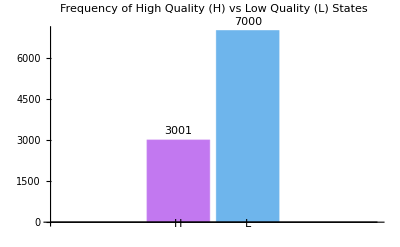

```mathematica
(*Continue from the previous simulation code*)(*Count occurrences of H and L*)occurrences=Counts[statesHistory];

(*Create a histogram from the occurrences*)
histogram=BarChart[Values[occurrences],ChartLabels->Keys[occurrences],PlotLabel->"Frequency of High Quality (H) vs Low Quality (L) States",ChartStyle->"Pastel",LabelingFunction->Above];

(*Display the histogram*)
histogram
```

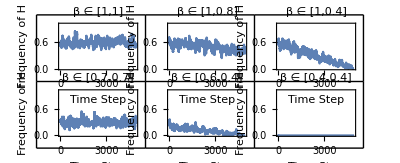

```mathematica
(*Parameters*)a=0.4;
timeSteps=5000;  (*Increase for detailed simulation*)
betaClasses={{1,1},{1,0.8},{1,0.4},{0.7,0.7},{0.6,0.4},{0.4,0.4}};

(*Function to simulate market behavior for a given β range*)
simulateMarketBehavior[βStart_,βEnd_]:=Module[{β,t,transitionMatrix,state,statesHistory},state="H";
statesHistory={state};
For[t=1,t<=timeSteps,t++,β=βStart-t*(βStart-βEnd)/timeSteps;
transitionMatrix={{β-a,1-(β-a)},{β-a,1-(β-a)}};
stateProbabilities=If[state=="H",transitionMatrix[[1]],transitionMatrix[[2]]];
state=If[RandomReal[]<stateProbabilities[[1]],"H","L"];
AppendTo[statesHistory,state];];
statesHistory];

(*Plot for each β class*)
plots=Table[statesHistory=simulateMarketBehavior[βClass[[1]],βClass[[2]]];
frequencyH=MovingAverage[Map[If[#=="H",1,0]&,statesHistory],50];(*50-step moving average for smoothness*)ListLinePlot[frequencyH,PlotRange->{0,1},PlotLabel->StringForm["β ∈ [``,``]",βClass[[1]],βClass[[2]]],Frame->True,FrameLabel->{"Time Step","Frequency of H"}],{βClass,betaClasses}];

(*Display the plots*)
GraphicsGrid[Partition[plots,3],Frame->All]
```

```mathematica
(*Modified Plot for each β class with initial expectation*)plotsWithExpectation=Table[statesHistory=simulateMarketBehavior[βClass[[1]],βClass[[2]]];
frequencyH=MovingAverage[Map[If[#=="H",1,0]&,statesHistory],50];
initialExpectation=βClass[[1]]-a;(*Initial expectation based on the starting β*)ListLinePlot[{frequencyH,(*The dynamic frequency of H over time*)Table[initialExpectation,{timeSteps}]  (*The initial expected frequency of H*)},PlotRange->{0,1},PlotLabel->StringForm["β ∈ [``,``]",βClass[[1]],βClass[[2]]],Frame->True,FrameLabel->{"Time Step","Frequency of H"},PlotLegends->{"Frequency of H","Initial Expectation of H"}],{βClass,betaClasses}];

(*Display the plots with expectations*)
GraphicsGrid[Partition[plotsWithExpectation,3],Frame->All]
```

-Graphics-